```mathematica
data = Import["C:\\Users\\Jesus Enrique\\Documents\\bookanalysis.csv"]
```

{{geographer,26200,209.384},{tippler,13400,596.767},{lamplighter,10200,197.025},{baobabs,6353,4097.68},{lamplighters,4257,78.7191},{constrictor,2975,967.153},{abashed,2975,823.779},{sprig,2380,11.3137},{shrugging,2000,0},{constrictors,1862,7788.59},{baobab,1587,857.75},{voluminous,1500,0},{tipplers,1500,0},2107,{living,0,0},{open,0,0},{crazy,0,0},{fun,0,0},{dead,0,0},{nice,0,0},{shuts,0,0},{watches,0,0},{yourselves,0,0},{saddest,0,0},{case,0,0},{refuses,0,0},{happen,0,0}}
 |  |  |  |

```mathematica
byWeight=Table[{data[[i,1]],data[[i,2]]},{i,1,Length[data]}];
byStdev=Table[{data[[i,1]],data[[i,3]]},{i,1,Length[data]}];
byStdevweight=Table[{data[[i,1]],data[[i,2]]*data[[i,3]]},{i,1,Length[data]}];
```

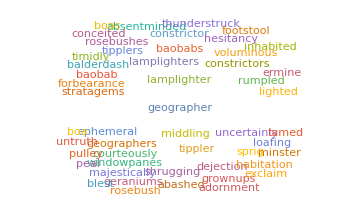

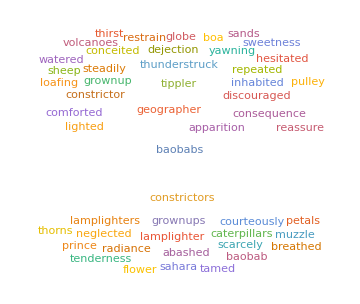

```mathematica
WordCloud[byWeight, MaxItems->50, ImageSize->Medium]
WordCloud[byStdevweight, MaxItems->50, ImageSize->Medium]
```

```mathematica
k1 = 1/Max[data[[;;,2]]]*100.
k2 = k1/10000
byParams = Table[{data[[i,1]],data[[i,2]] *(k1 + k2 data[[i,3]])},{i,1,Length[data]}];
WordCloud[byParams, MaxItems->50, ImageSize->Medium]
```

0.00381679

3.81679×10^-7

WordCloud::nomem: Not enough memory available to compute the word cloud.

WordCloud[{{geographer,102.094},{tippler,54.1972},{lamplighter,39.6983},{baobabs,34.1842},{lamplighters,16.376},{constrictor,12.4532},{abashed,12.2904},{sprig,9.09425},{shrugging,7.63359},{constrictors,12.6421},{baobab,6.57681},{voluminous,5.72519},2110,{crazy,0.},{fun,0.},{dead,0.},{nice,0.},{shuts,0.},{watches,0.},{yourselves,0.},{saddest,0.},{case,0.},{refuses,0.},{happen,0.}},1,1]
 |  |  |  |